# ACM 11 HW 3 Ty Limpasuvan

```mathematica
(* 1.1 *)
x = 354224848179261915075;
!SquareFreeQ[5 * x^2 + 4]  || !SquareFreeQ[5 * x^2 - 4]
```

True

```mathematica
(* 1.2 *)
x = 2305843008138952128;
DivisorSigma[1,x] == 2 * x
```

False

```mathematica
(* 1.3 *)
NextPrime[1000000000]
```

1000000007

```mathematica
(* 1.4 *)
SetPrecision[ZetaZero[20],100]
```

0.5+77.14484006887480537268266485630463701579603244923446104176523145315113916425371508940828869469973776 ⅈ

```mathematica
(* 1.5 *)
Sum[(3^k - 1) * Zeta[k + 1]/ (4^k),{k, 1, Infinity}]
```

π

```mathematica
(* 2.1 *)
V[n_,R_] := (Pi^(n / 2) * R^n) / Gamma[(n / 2) + 1]
S[n_, R_] := ((n  + 1) * Pi^((n + 1) / 2) * R^n) / Gamma[((n + 1) / 2) + 1]
```

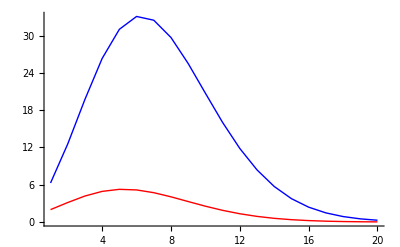

```mathematica
(* 2.2 *)
Show[ListLinePlot[Table[V[n, 1], {n, 1, 20}], PlotStyle->{Red, Thick}],
ListLinePlot[Table[S[n, 1], {n, 1, 20}], PlotStyle ->{Blue, Thick}] , PlotRange->Automatic]
```

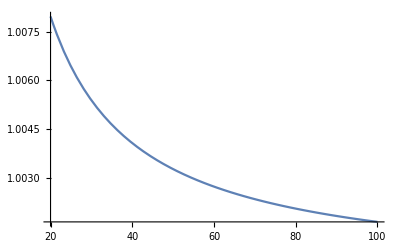

```mathematica
(* 2.3 *)
GammaApprox[n_] := Sqrt[2 * Pi] * E ^ (-n/ 2) * (n /2)^((n + 1) / 2);
OverTilde[S][n_, R_] := (n+1)*Pi^((n + 1) / 2)*R^n/ GammaApprox[n + 1];

Plot[OverTilde[S][n, 1] / S[n, 1], {n, 20, 100}] (* This is independent of the value of R *)
```

```mathematica
(* 2.4 *)
points = RandomReal[{0, 1}, {10^6, 10}];
dist =Map[Norm, points];
cnt = Count[dist, x_/; x <= 1];
n =((cnt / 10^6)* 2^10 * Gamma[6])^(1/5)//N
```

3.15252

```mathematica
(* Error *)
((n - Pi) / Pi) * 100 (* Percent *)
```

0.347762

```mathematica
(* 3.1 *)
mandelbrot[cx_, cy_, nmax_]:= 
Module[{curr = 0,m = 1}, 
 While[Abs[curr] ≤ 2&&m < nmax,
curr = curr ^ 2 + cx + cy * ⅈ;
m = m+1;
];
m
]
```

```mathematica
(* 3.2 *)
mandelbrot[Sqrt[5]/100, 0, 1000]
```

1000

```mathematica
mandelbrotC = Compile[{cx, cy, nmax}, mandelbrot[cx, cy, nmax]]
```

CompiledFunction[…]

```mathematica
mandelbrotC[Sqrt[5]/100, 0, 1000]
```

1000.

```mathematica
(* 3.3 *)
DensityPlot[-mandelbrotC[cx, cy, 100], {cx, -2,0.6}, {cy, -1.3, 1.3}, ColorFunction->GrayLevel, PlotPoints->100]
```

-Graphics-

```mathematica
(* 3.4 *)
DensityPlot[-mandelbrotC[cx, cy, 100], {cx, -0.4,0.1}, {cy, 0.6, 1.1}, PlotPoints->100]
```

-Graphics-

```mathematica
DensityPlot[-mandelbrotC[cx, cy, 1000], {cx, -0.75,-0.747}, {cy, 0.06, 0.063}, PlotPoints->300, ImageSize->Large]
```

-Graphics-